## Data

```mathematica
SetDirectory[NotebookDirectory[]];
datasets={"Ocean","Drosophila_Gut","Soil_Vitro","Soil_Vivo","Human_Oral","Human_Gut"};
```

```mathematica
tst = Table[Flatten@Import["../Results/Experimental/"<>d<>"/test_loss.csv"],{d,datasets}];
trn = Table[Flatten@Import["../Results/Experimental/"<>d<>"/train_loss.csv"],{d,datasets}];
tstN = Table[Flatten@Import["../Results/Experimental/"<>d<>"/null_model/test_loss.csv"],{d,datasets}];
trnN = Table[Flatten@Import["../Results/Experimental/"<>d<>"/null_model/train_loss.csv"],{d,datasets}];
```

```mathematica
real = Table[Transpose@Import["../Results/Experimental/"<>d<>"/real_sample.csv"],{d,datasets}];
pred = Table[Transpose@Import["../Results/Experimental/"<>d<>"/pred_sample.csv"],{d,datasets}];
realN = Table[Import["../Results/Experimental/"<>d<>"/null_model/real_sample.csv"],{d,datasets}];
predN = Table[Import["../Results/Experimental/"<>d<>"/null_model/pred_sample.csv"],{d,datasets}];
```

```mathematica
discreteColors[n_]:=With[{partL=Ceiling[Sqrt[n]]},DeleteCases[Flatten[Transpose[Partition[Table[Lighter[Darker[Hue[c],.1],.25],{c,0,1-1/n,1/n}],partL,partL,1,0]]],0]]
```

## Box plots

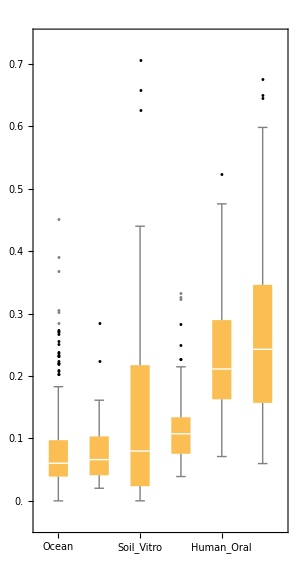

```mathematica
BoxWhiskerChart[Thread@{tst},"Outliers",
FrameTicks->{{Range[0,1,0.05],None},{All,None}},
FrameTicksStyle->14,
ChartLabels->{Rotate[Style["\n"<>#,10],45Degree]&/@datasets,None},
AspectRatio->1.2GoldenRatio,ImageSize->300]
```

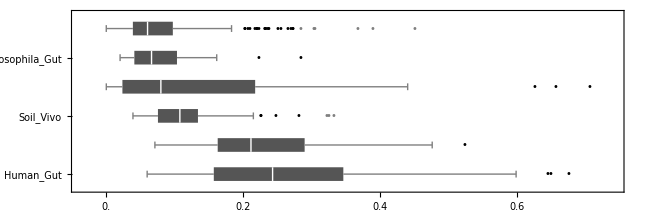

```mathematica
BoxWhiskerChart[Reverse[Thread@{tst}],"Outliers",
FrameTicks->{{Range[0,1,0.05],None},{Range[0,1,0.1],None}},
FrameTicksStyle->13,
BarOrigin->Left,
ChartStyle->Darker@Gray,
ChartLabels->{Rotate[Style["\n"<>#,10],45Degree]&/@(Reverse@datasets),None},
AspectRatio->0.2GoldenRatio,ImageSize->650]
```

## Visualize samples

### Drosophila

```mathematica
Manipulate[
Module[{k,order,colors},
k=1;
colors=discreteColors[Length[pred⟦k⟧]];
order = Ordering[tst⟦k⟧];
BarChart[{real⟦k⟧⟦All,order⟦i⟧⟧,pred⟦k⟧⟦All,order⟦i⟧⟧},
ChartLabels->{Placed[{"true","predicted"},Axis],None},
ChartLayout->"Stacked",
BarOrigin->Left,
FrameTicksStyle->16,
ImageSize->200,
BarSpacing->0.2,
ChartStyle->colors,
AspectRatio->0.5/GoldenRatio,
PlotLabel->"error= "<>ToString[tst⟦k⟧⟦order⟦i⟧⟧],ImageSize->Large]],
{i,1,Length@tst⟦1⟧,1},SaveDefinitions->True]
```

### Ocean

```mathematica
Manipulate[
Module[{k,order},
k=2;
order = Ordering[tst⟦k⟧];
BarChart[{real⟦k⟧⟦All,order⟦i⟧⟧,pred⟦k⟧⟦All,order⟦i⟧⟧},
ChartLabels->{Placed[{"true","predicted"},Axis],None},
ChartLayout->"Stacked",
BarOrigin->Left,
FrameTicksStyle->16,
ImageSize->200,
BarSpacing->0.2,
ChartStyle->{
Directive[RGBColor[0, 0.6900000000000001, 1]],
Directive[RGBColor[1, 0.29, 0.5]],
Directive[RGBColor[1, 0.76, 0]],
Directive[RGBColor[0, 0.78, 0]],
Directive[RGBColor[0.61, 0, 0.92]]
},
AspectRatio->0.5/GoldenRatio,
PlotLabel->"error= "<>ToString[tst⟦k⟧⟦order⟦i⟧⟧],ImageSize->Large]],
{i,1,Length@tst⟦2⟧,1},SaveDefinitions->True]
```

### Soil in vitro

```mathematica
Manipulate[
Module[{k,order},
k=3;
order = Ordering[tst⟦k⟧];
BarChart[{real⟦k⟧⟦All,order⟦i⟧⟧,pred⟦k⟧⟦All,order⟦i⟧⟧},
ChartLabels->{Placed[{"true","predicted"},Axis],None},
ChartLayout->"Stacked",
BarOrigin->Left,
FrameTicksStyle->16,
ImageSize->200,
BarSpacing->0.2,
ChartStyle->54,
AspectRatio->0.5/GoldenRatio,
PlotLabel->"error= "<>ToString[tst⟦k⟧⟦order⟦i⟧⟧],ImageSize->Large]],
{i,1,Length@tst⟦3⟧,1},SaveDefinitions->True]
```

### Soil in vivo

```mathematica
Manipulate[
Module[{k,order},
k=4;
order = Ordering[tst⟦k⟧];
BarChart[{real⟦k⟧⟦All,order⟦i⟧⟧,pred⟦k⟧⟦All,order⟦i⟧⟧},
ChartLabels->{Placed[{"true","predicted"},Axis],None},
ChartLayout->"Stacked",
BarOrigin->Left,
FrameTicksStyle->16,
ImageSize->200,
BarSpacing->0.2,
ChartStyle->54,
AspectRatio->0.5/GoldenRatio,
PlotLabel->"error= "<>ToString[tst⟦k⟧⟦order⟦i⟧⟧],ImageSize->Large]],
{i,1,Length@tst⟦4⟧,1},SaveDefinitions->True]
```

### Human Oral

```mathematica
Manipulate[
Module[{k,order,colors},
k=5;
colors=discreteColors[Length[pred⟦k⟧]];
order = Ordering[tst⟦k⟧];
BarChart[{real⟦k⟧⟦All,order⟦i⟧⟧,pred⟦k⟧⟦All,order⟦i⟧⟧},
ChartLabels->{Placed[{"true","predicted"},Axis],None},
ChartLayout->"Stacked",
BarOrigin->Left,
FrameTicksStyle->16,
ImageSize->200,
BarSpacing->0.2,
ChartStyle->colors,
AspectRatio->0.5/GoldenRatio,
PlotLabel->"error= "<>ToString[tst⟦k⟧⟦order⟦i⟧⟧],ImageSize->Large]],
{i,1,Length@tst⟦5⟧,1},SaveDefinitions->True]
```

### Human Gut

```mathematica
Manipulate[
Module[{k,order,colors},
k=6;
colors=discreteColors[Length[pred⟦k⟧]];
order = Ordering[tst⟦k⟧];
BarChart[{real⟦k⟧⟦All,order⟦i⟧⟧,pred⟦k⟧⟦All,order⟦i⟧⟧},
ChartLabels->{Placed[{"true","predicted"},Axis],None},
ChartLayout->"Stacked",
BarOrigin->Left,
FrameTicksStyle->16,
ImageSize->200,
BarSpacing->0.2,
ChartStyle->colors,
AspectRatio->0.5/GoldenRatio,
PlotLabel->"error= "<>ToString[tst⟦k⟧⟦order⟦i⟧⟧],ImageSize->Large]],
{i,1,Length@tst⟦6⟧,1},SaveDefinitions->True]
```

## Correlation plots

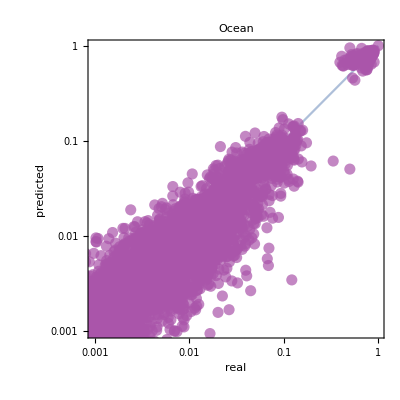
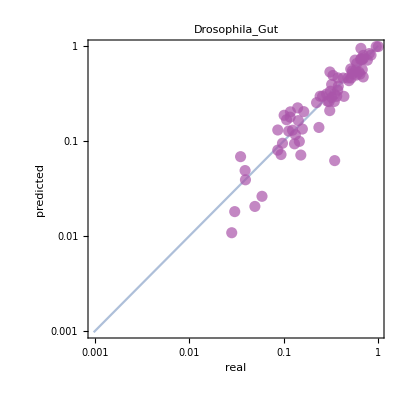
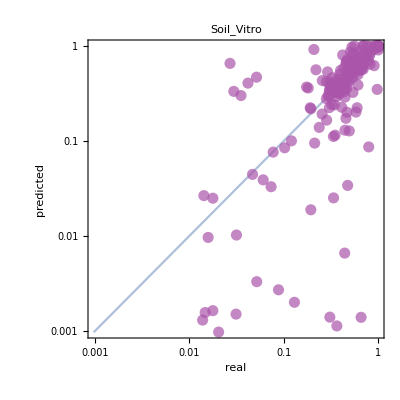
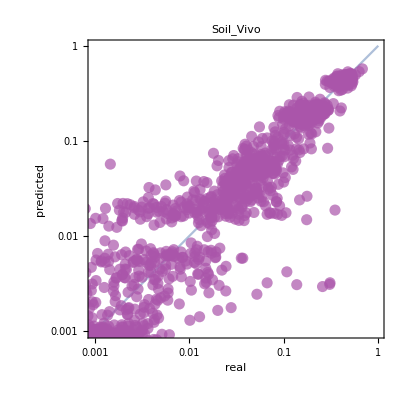
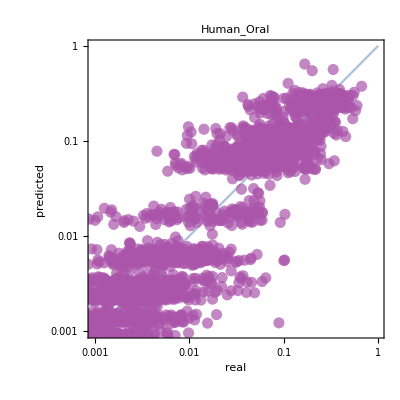
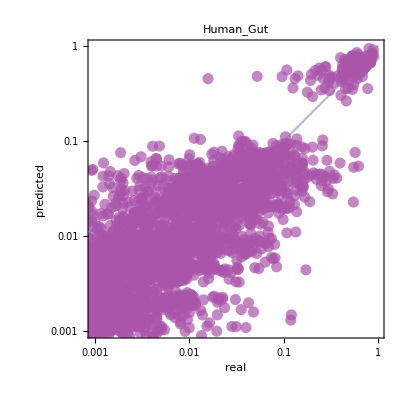

```mathematica
titles = {"ocean","drosophila gut","in vitro soil","in vivo soil","human oral","human gut"};
plts = Table[Show[
LogLogPlot[x,{x,0,1},PlotStyle->Opacity[0.5],PlotRange->{{0,1},{0,1}},Frame->True,AspectRatio->1,FrameLabel->{"real (log)","predicted (log)"},PlotLabel->titles[[i]]],
ListLogLogPlot[Thread[{Flatten[real[[i]]],Flatten[pred[[i]]]}],PlotStyle->{PointSize[0.02],Opacity[0.7],Lighter@Purple}]
],{i,1,Length@datasets}]
```